## Many Harmonic Oscillators

## Completed and Analyzed in class, February 21, 2025

This is the ninth notebook for you to complete.

### Seven Oscillators — Formulas for the Accelerations

At the end of the Coupled Harmonic Oscillators - Theory writeup, I pointed to where we were going to go after doing two oscillators. For five equal masses connected to each other and the walls by six identical springs, we have:

a_1=-ω_0^2(x_1-0)+ω_0^2(x_2-x_1)

a_2=-ω_0^2(x_2-x_1)+ω_0^2(x_3-x_2)
 
a_3=-ω_0^2(x_3-x_2)+ω_0^2(x_4-x_3)

a_4=-ω_0^2(x_4-x_3)+ω_0^2(x_5-x_4)

a_5=-ω_0^2(x_5-x_4)+ω_0^2(0-x_5)

where

ω_0^2≡k/m

As you can see, I have done some small but suggestive rewrites to make the five equations appear more similar to each other. The left-most and right-most oscillators have equations that don’t quite fit the pattern due to their connection to the walls. The walls can’t move. Their lack of movement is captured in the 0’s that I have suggestively placed into the amount the two end springs are stretched.

### Why Stop at Five — Formulas for the Accelerations of Many Oscillators

Let’s have n masses and n+1 springs. For starters, let’s do n=5, but later on, we can make n whatever we like. Let’s also define ω_0 while we are at it:

```mathematica
n=5;
omega0=2Pi;
```

It is most definitely not going to cut it to have to write out an equation for the acceleration of each of the n masses. Sure we could write out all five equations for all five masses if there are only five, but if we don’t want to exhaust ourselves doing error-prone copy-and-paste operations when we get to larger values of n, we are going to have to be craftier.

The trick is to number the masses and have that number be part of the acceleration equation. We will index the oscillators by j and j can take on any value from 1 to n (I’d use i again, but we are already using i for the time steps, and it might be confusing to people to re-use that letter). The next formula is almost right. Examine it and figure out what is wrong with it.

```mathematica
wrongEquationsForAcceleration[j_,allPositions_]:=
-omega0^2(allPositions[[j]]-allPositions[[j-1]])+omega0^2(allPositions[[j+1]]-allPositions[[j]])
```

We need to handle the left-most and right-most oscillators (the ones that are next to the walls) specially. That’s going to require some If[] statements:

```mathematica
acceleration[j_,allPositions_]:=
-omega0^2(allPositions[[j]]-If[j==1, 0, allPositions[[j-1]]])+omega0^2(If[j==n,0,allPositions[[j+1]]]-allPositions[[j]])
```

### Initial Conditions

First set up the duration:

```mathematica
tInitial = 0.0;
tFinal = 10.0;
```

Here are five sets of initial conditions (these are known as eigenvectors and the omegas are known as eigenvalues) that are very particular to the case n=5:

```mathematica
iA5={
{1/(2Sqrt[3]),1/2,1/Sqrt[3],1/2,1/(2Sqrt[3])},
{1/2,1/2,0,-1/2,-1/2},
{1/Sqrt[3],0,-1/Sqrt[3],0,1/Sqrt[3]},
{1/2,-1/2,0,1/2,-1/2},
{1/(2Sqrt[3]),-1/2,1/Sqrt[3],-1/2,1/(2Sqrt[3])}
};
omega5={Sqrt[1/(2+Sqrt[3])],1/Sqrt[3],1/Sqrt[2],1,Sqrt[1/(2-Sqrt[3])]}omega0;
```

We’ll use them after we have the notebooks working. For now, just do this more simple-minded initial condition:

```mathematica
pluck=-0.5;
initialPositions={0.0,pluck,0.0,0.0,0.0};
initialVelocities=Table[0.0,n];
```

### A List Containing Lists!

We have a decision to make on how we are packing the time, the positions, and the velocities into the initial conditions list, but here is the obvious choice:

```mathematica
initialConditions={tInitial,initialPositions,initialVelocities};
```

### Second-Order Runge-Kutta — Formulas for n Particles

t_(i+1)=t_i+Δt

x_j^*=x_j(t_i)+v_j(t_i)·Δt/2       (j goes from 1 to n)

v_j(t_(i+1))=v_j(t_i)+a_j(that depends on neighboring x^*)·Δt

x_j(t_(i+1))=x_j(t_i)+ (v_j(t_i)+v_j(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementing the Formulas

```mathematica
steps = 2000;
deltaT = (tFinal - tInitial)/steps;

rungeKutta2[cc_]:= (
curTime=cc[[1]];
curPositions=cc[[2]];
curVelocities=cc[[3]];
newTime=curTime+deltaT;
xStars=curPositions+curVelocities deltaT/2;
accelerations=Table[acceleration[j,xStars],{j,n}];
newVelocities=curVelocities+accelerations deltaT;
newPositions=curPositions+(curVelocities+newVelocities)deltaT/2;
{newTime,newPositions,newVelocities}
)
(* Test your implementation on the initial conditions *)
N[rungeKutta2[initialConditions]]
(* This is what I get: *)
(* {0.005, {-0.00024674, -0.499507, -0.00024674, 0., 0.}, {-0.098696, 0.197392, -0.098696, 0., 0.}} *)
```

{0.005,{-0.00024674,-0.499507,-0.00024674,0.,0.},{-0.098696,0.197392,-0.098696,0.,0.}}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
rk2ResultsTransposed=Transpose[rk2Results];
positionLists=rk2ResultsTransposed[[2]];
```

#### A Graphic

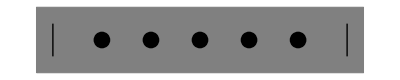

```mathematica
coupledOscillatorGraphic[positionList_]:=Graphics[{
width=10;
buffer=0.5;
netWidth=width-2 buffer;
wallHeight=1.0;
numberOfSprings=n+1;
(* the next line makes a gray rectangle *)
{EdgeForm[Thin],Gray,Polygon[{{0,-1},{width,-1},{width,1},{0,1}}]},
(* the next two lines make the walls *)
Line[{{buffer,-wallHeight/2},{buffer,wallHeight/2}}],
Line[{{width-buffer,-wallHeight/2},{width-buffer,wallHeight/2}}],
(* finally we draw all the points *)
Table[Style[Point[{positionList[[j]]+netWidth/numberOfSprings j+buffer,0.0}],PointSize[0.03]],{j,n}]
}]
(* A little test to see if our code at least draws equally-spaced points when the positions are all zero: *)
coupledOscillatorGraphic[Table[0.0,n]]
```

#### Animating The Graphics

```mathematica
Animate[coupledOscillatorGraphic[positionLists[[i]]],{i,1,steps,1}, DefaultDuration->tFinal-tInitial]
```

#### Things to Try Once the Notebook is Working

```mathematica
(* Go back up to the initial conditions section, and where it said: *)
(* initialPositions={0.0,-pluck,0.0,0.0,0.0}; *)
(* Change that line to one of the special initial conditions. *)
(* initialPositions=iA5[[1]]; *)
(* initialPositions=iA5[[2]]; *)
(* initialPositions=iA5[[3]]; *)
(* initialPositions=iA5[[4]]; *)
(* or *)
(* initialPositions=iA5[[5]]; *)
(* All of these are interesting! *)
(* When you are done, change it back to what it originally was. *)

(* A completely different thing to try is to change the graphics. *)
(* Make the masses bob up and down instead of left to right. *)
(* You might view this as an improvement and just leave it that way. *)

(* Yet another thing to try is to mess with the acceleration formula *)
(* acceleration[j_,allPositions_]:= *)
(*   -omega0^2(allPositions[[j]]-If[j==1, 0, allPositions[[j-1]]])+omega0^2(If[j==n,0,allPositions[[j+1]]]-allPositions[[j]]) *)
(* The thing to change is the first 0 to allPositions[[n]] and the second 0 to allPositions[[1]] *)
(* Physically, what that is doing is eliminating the walls and connecting the right-most mass to the left-most mass. *)
(* This is called "periodic boundary conditions." When you are done, put the walls back in by changing the zeros back. *)

(* I have been experimenting around trying to make other more regular-looking patterns, *)
(* but I have been unsuccessful. The code I was trying had special values for the *)
(* initial velocities, and it looked like this: *)
(* innerProducts = Table[Dot[initialPositions,iA5[[k]]],{k,5}]; *)
(* weightediA5=-Table[iA5[[k]]innerProducts[[k]]omega5[[k]],{k,5}]; *)
(* initialVelocities=N[Total[weightediA5]] *)
(* Since I have been unsuccessful, I recommend skipping to my next and last idea that follows. *)

(* The last idea is to take much larger values of n. The initial *)
(* conditions line that looks like this will have to be rewritten: *)
(* initialPositions={0.0,pluck,0.0,0.0,0.0}; *)
(* since it assumed n=5, and so it is useless for other values of n. It is a small but good *)
(* exercise to make that code work for any n. Don't just copy-and-paste 999 zeros to get n=1000. *)
(* A good amount to try is n=100. Drop the point size from 0.3 to 0.005 so the dots weren't crowding *)
(* each other, increase the animation time from 10.0 to 40.0, and increase the steps from 2000 to 8000. *)
(* Finally, I'd recommend combining this with the idea of making the masses bob up and down *)
(* instead of left to right because otherwise they overlap each other in an illegible way. *)
(* If you do all that, you'll finally see something wave-like appear. It is admittedly still jumbled, *)
(* but there are very good physical reasons for this! We've done enough with coupled harmonic oscillators, *) 
(* and although the physics and the equations are almost identical, after the Term 4-5 break, when *)
(* we get to the torsion pendulum and coupled torsion pendula, we'll take the time to start understanding *)
(* and minimizing the jumbling so that we can more clearly see waves emerging. *)
```